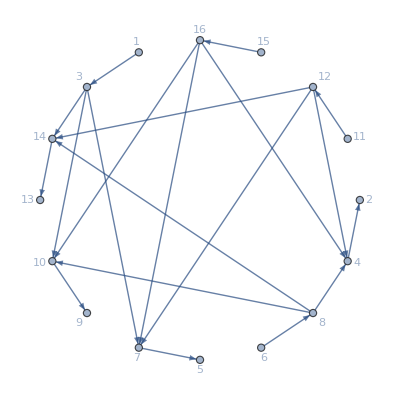

```mathematica
Graph[{1->3,3->7,7->5,3->10,10->9,3->14,14->13,6->8,8->4,4->2,8->10,8->14,11->12,12->4,12->7,12->14,15->16,16->4,16->7,16->10},GraphLayout->"CircularEmbedding",VertexLabels->"Name"]
```

### How to blow up the graph

```mathematica
Clear[C]
```

Clear::wrsym: Symbol C is Protected.

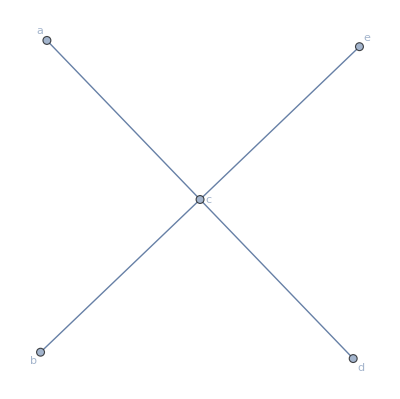

```mathematica
Graph[{a<->c,b<->c,c<->d,c<->e},GraphLayout->"SpringEmbedding",VertexLabels->Automatic]
```

#### joined the corresponding ends with undirected graph to make it look better...

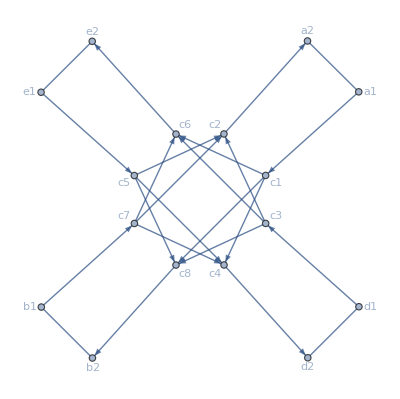

```mathematica
Graph[{a1->c1,c2->a2,d1->c3,c4->d2,e1->c5,c6->e2,b1->c7,c8->b2,c1->c4,c1->c6,c1->c8,c3->c2,c3->c6,c3->c8,c5->c2,c5->c4,c5->c8,c7->c2,c7->c4,c7->c6,a1<->a2,b1<->b2,d1<->d2,e1<->e2},GraphLayout->"SpringElectricalEmbedding",VertexLabels->Automatic]
```

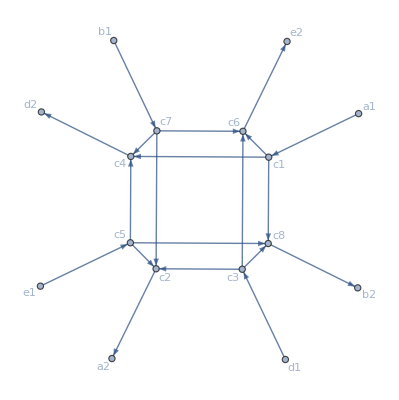

```mathematica
Graph[{a1->c1,c2->a2,d1->c3,c4->d2,e1->c5,c6->e2,b1->c7,c8->b2,c1->c4,c1->c6,c1->c8,c3->c2,c3->c6,c3->c8,c5->c2,c5->c4,c5->c8,c7->c2,c7->c4,c7->c6},GraphLayout->"SpringEmbedding",VertexLabels->Automatic]
```

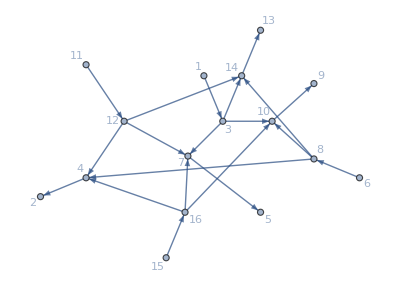

```mathematica
Graph[{1->3,3->7,7->5,3->10,10->9,3->14,14->13,6->8,8->4,4->2,8->10,8->14,11->12,12->4,12->7,12->14,15->16,16->4,16->7,16->10},GraphLayout->"RadialEmbedding",VertexLabels->"Name"]
```

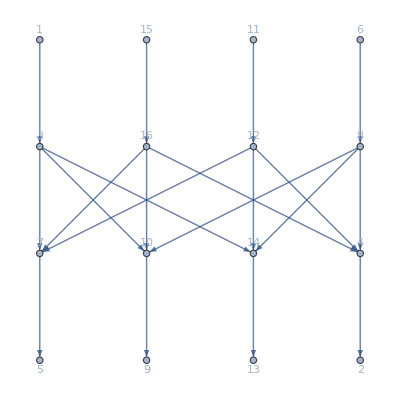

```mathematica
Graph[{1->3,3->7,7->5,3->10,10->9,3->14,14->13,6->8,8->4,4->2,8->10,8->14,11->12,12->4,12->7,12->14,15->16,16->4,16->7,16->10},GraphLayout->"LayeredDigraphEmbedding",VertexLabels->"Name"]
```

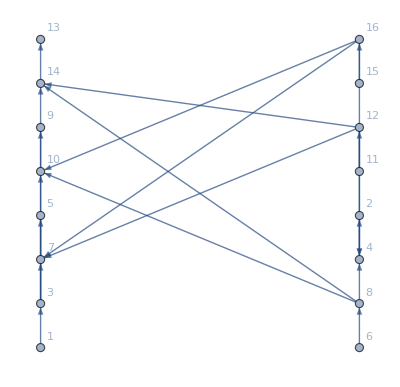

```mathematica
Graph[{1->3,3->7,7->5,3->10,10->9,3->14,14->13,6->8,8->4,4->2,8->10,8->14,11->12,12->4,12->7,12->14,15->16,16->4,16->7,16->10},GraphLayout->"MultipartiteEmbedding",VertexLabels->"Name"]
```

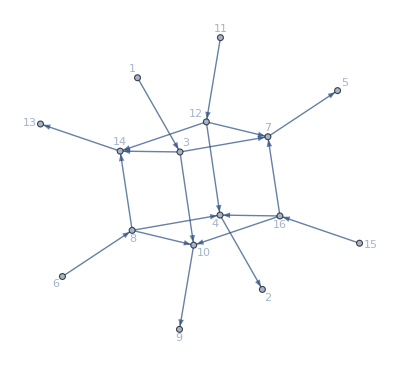

```mathematica
Graph[{1->3,3->7,7->5,3->10,10->9,3->14,14->13,6->8,8->4,4->2,8->10,8->14,11->12,12->4,12->7,12->14,15->16,16->4,16->7,16->10},GraphLayout->"SpringElectricalEmbedding",VertexLabels->"Name"]
```

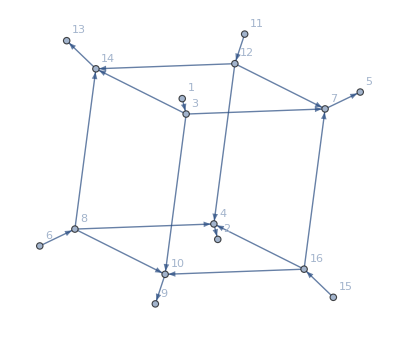

```mathematica
Graph[{1->3,3->7,7->5,3->10,10->9,3->14,14->13,6->8,8->4,4->2,8->10,8->14,11->12,12->4,12->7,12->14,15->16,16->4,16->7,16->10},GraphLayout->"HighDimensionalEmbedding",VertexLabels->"Name"]
```

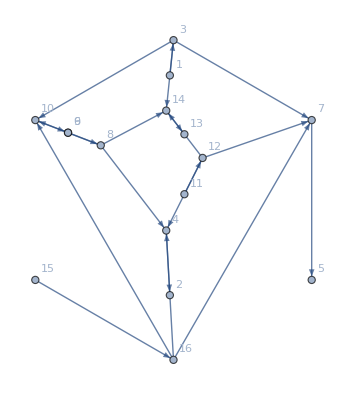

```mathematica
Graph[{1->3,3->7,7->5,3->10,10->9,3->14,14->13,6->8,8->4,4->2,8->10,8->14,11->12,12->4,12->7,12->14,15->16,16->4,16->7,16->10},GraphLayout->"TutteEmbedding",VertexLabels->"Name"]
```